Úloha 1:

{{x→Function[{t},ⅇ^t]}}

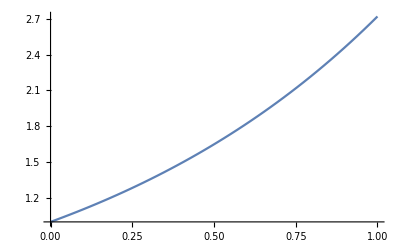

```mathematica
DSolve[{x'[t]==x[t], x[0]==1}, x, t]
Plot[Evaluate[x[t]/.%], {t, 0,1}]
```

{{x→Function[{t},1/(2-t)]}}

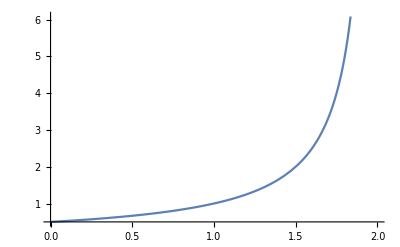

```mathematica
DSolve[{x'[t]==x[t]^2, x[0]==1/2}, x, t]
Plot[Evaluate[x[t]/.%], {t, 0,2}]
```

{{x→Function[{t},-√2 √t]},{x→Function[{t},√2 √t]}}

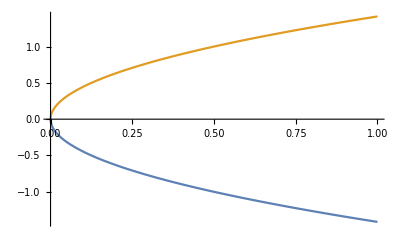

```mathematica
DSolve[{x'[t]==1/x[t], x[0]==0}, x, t]
Plot[Evaluate[x[t]/.%], {t, 0,1}]
```

{{x→Function[{t},1/4 (-1+5 ⅇ^(2 t)-2 t-2 t^2)]}}

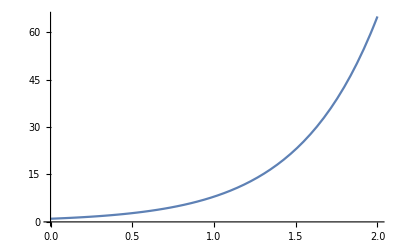

```mathematica
DSolve[{x'[t]==2x[t]+t^2, x[0]==1}, x, t]
Plot[Evaluate[x[t]/.%], {t, 0,2}]
```

Úloha 2:

```mathematica
DSolve[{x'[t]==e^(x[t]^2), x[0]==1/2}, x, t]
Plot[Evaluate[x[t]/.%], {t, 0,1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Function[{t},InverseErf[(2 (1/2 √π Erf[(√Log[e])/2]+t √Log[e]))/(√π)]/(√Log[e])]}}

-Graphics-

{{x→InterpolatingFunction[…]}}

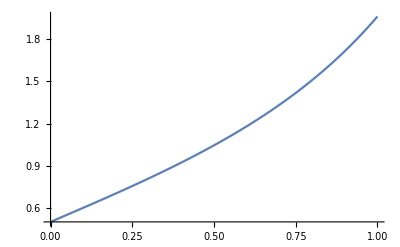

```mathematica
NDSolve[{x'[t]==Exp[t^2], x[0]==1/2}, x, {t, 0, 1}]
Plot[Evaluate[x[t]/.%], {t, 0,1}]
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity ProductLog[-ⅇ^(1/50)/50]/(1+ProductLog[-ⅇ^(1/50)/50])-(50 ProductLog[-ⅇ^(1/50)/50])/(50+50 ProductLog[-1/50 Power[«2»]]) is equal to zero. Assuming it is.

{{x→Function[{t},50 ProductLog[1/50 (ⅇ^(1+t))^(1/50)]]}}

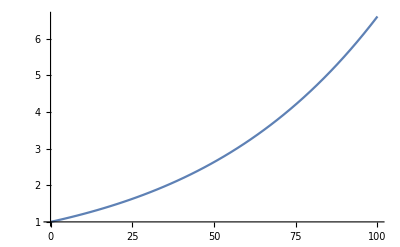

```mathematica
DSolve[{x'[t]==x[t]/(x[t]+50), x[0]==1}, x, t]
Plot[Evaluate[x[t]/.%], {t, 0,100}]
```

```mathematica
NDSolve[{x'[t]==x[t]/(x[t]+50), x[0]==1}, x, {t,0,100}]
Plot[Evaluate[x[t]/.%], {t, 0,100}]
```

{{x→InterpolatingFunction[…]}}

-Graphics-

Úloha 3:

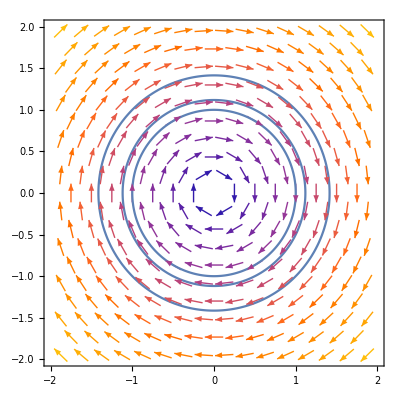

```mathematica
NDSolve[{x'[t]==y[t],y'[t]==-x[t],x[0]==1,y[0]==1},{x,y},{t,0,2π}];
p1 = ParametricPlot[Evaluate[{x[t],y[t]}/. %],{t, 0,2π}];
NDSolve[{x'[t]==y[t],y'[t]==-x[t],x[0]==1/2,y[0]==1},{x,y},{t,0,2π}];
p2=ParametricPlot[Evaluate[{x[t],y[t]}/. %],{t, 0,2π}];
NDSolve[{x'[t]==y[t],y'[t]==-x[t],x[0]==1,y[0]==0},{x,y},{t,0,2π}];
p3=ParametricPlot[Evaluate[{x[t],y[t]}/. %],{t, 0,2π}];
Show[
VectorPlot[{y,-x},{x,-2,2},{y,-2,2}],
p1,p2, p3
]
```

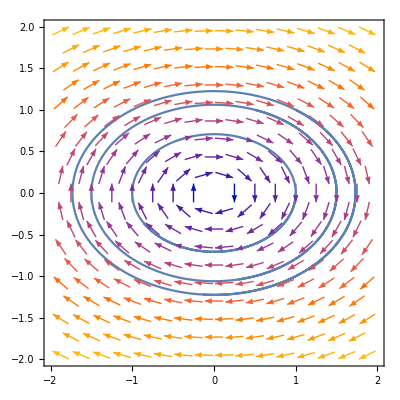

```mathematica
NDSolve[{x'[t]==2y[t],y'[t]==-x[t],x[0]==1,y[0]==1},{x,y},{t,0,2π}];
p1 = ParametricPlot[Evaluate[{x[t],y[t]}/. %],{t, 0,2π}];
NDSolve[{x'[t]==2y[t],y'[t]==-x[t],x[0]==1/2,y[0]==1},{x,y},{t,0,2π}];
p2=ParametricPlot[Evaluate[{x[t],y[t]}/. %],{t, 0,2π}];
NDSolve[{x'[t]==2y[t],y'[t]==-x[t],x[0]==1,y[0]==0},{x,y},{t,0,2π}];
p3=ParametricPlot[Evaluate[{x[t],y[t]}/. %],{t, 0,2π}];
Show[
VectorPlot[{2y,-x},{x,-2,2},{y,-2,2}],
p1,p2, p3
]
```

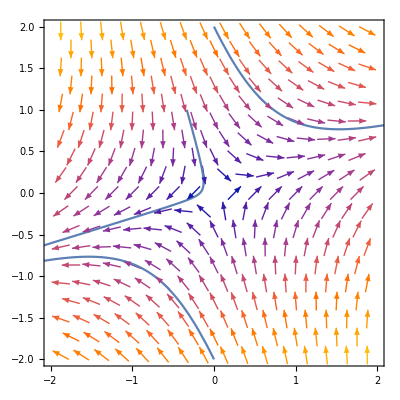

```mathematica
NDSolve[{x'[t]==x[t]+y[t],y'[t]==x[t]-2y[t],x[0]==0,y[0]==2},{x,y},{t,0,5}];
p1 = ParametricPlot[Evaluate[{x[t],y[t]}/. %],{t, 0,5}];
NDSolve[{x'[t]==x[t]+y[t],y'[t]==x[t]-2y[t],x[0]==0,y[0]==-2},{x,y},{t,0,5}];
p2=ParametricPlot[Evaluate[{x[t],y[t]}/. %],{t, 0,5}];
NDSolve[{x'[t]==x[t]+y[t],y'[t]==x[t]-2y[t],x[0]==-1/3,y[0]==1/1},{x,y},{t,0,5}];
p3=ParametricPlot[Evaluate[{x[t],y[t]}/. %],{t, 0,5}];
Show[
VectorPlot[{y+x,x-2y},{x,-2,2},{y,-2,2}],
p1,p2, p3
]
```

```mathematica
pp={{1,1,-1},{-1,-1,0},{0,1,-1}};
v={y[t], z[t],x[t]};
NDSolve[{x'[t]==v[[1]],y'[t]==v[[2]], z'[t]==v[[3]],x[0]==pp[[1]][[1]],y[0]==pp[[1]][[2]], z[0]==pp[[1]][[3]]},{x,y,z},{t,0,10}];
p1 = ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. %],{t, 0,5}];
NDSolve[{x'[t]==v[[1]],y'[t]==v[[2]], z'[t]==v[[3]],x[0]==pp[[2]][[1]],y[0]==pp[[2]][[2]], z[0]==pp[[2]][[3]]},{x,y,z},{t,0,10}];
p2 = ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. %],{t, 0,5}];
NDSolve[{x'[t]==v[[1]],y'[t]==v[[2]], z'[t]==v[[3]],x[0]==pp[[3]][[1]],y[0]==pp[[3]][[2]], z[0]==pp[[3]][[3]]},{x,y,z},{t,0,10}];
p3 = ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. %],{t, 0,5}];

Show[
VectorPlot3D[{y,z, x},{x,-2,2},{y,-2,2}, {z, -2,2}],
p1, p2, p3
]
```

-Graphics3D-

```mathematica
pp={{1,1,-1},{-1,-1,0},{0,1,-1}};
v={y[t]+z[t], x[t]+z[t],x[t]+y[t]};
NDSolve[{x'[t]==v[[1]],y'[t]==v[[2]], z'[t]==v[[3]],x[0]==pp[[1]][[1]],y[0]==pp[[1]][[2]], z[0]==pp[[1]][[3]]},{x,y,z},{t,0,10}];
p1 = ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. %],{t, 0,5}];
NDSolve[{x'[t]==v[[1]],y'[t]==v[[2]], z'[t]==v[[3]],x[0]==pp[[2]][[1]],y[0]==pp[[2]][[2]], z[0]==pp[[2]][[3]]},{x,y,z},{t,0,10}];
p2 = ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. %],{t, 0,5}];
NDSolve[{x'[t]==v[[1]],y'[t]==v[[2]], z'[t]==v[[3]],x[0]==pp[[3]][[1]],y[0]==pp[[3]][[2]], z[0]==pp[[3]][[3]]},{x,y,z},{t,0,10}];
p3 = ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. %],{t, 0,5}];

Show[
VectorPlot3D[{y,z, x},{x,-2,2},{y,-2,2}, {z, -2,2}],
p1, p2, p3
]
```

-Graphics3D-

```mathematica
pp={{1,1,-1},{-1,0,0},{0,1,-1}};
v={x[t]+y[t]+5z[t], x[t]+y[t]+z[t],x[t]+y[t]+z[t]};
NDSolve[{x'[t]==v[[1]],y'[t]==v[[2]], z'[t]==v[[3]],x[0]==pp[[1]][[1]],y[0]==pp[[1]][[2]], z[0]==pp[[1]][[3]]},{x,y,z},{t,0,10}];
p1 = ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. %],{t, 0,5}];
NDSolve[{x'[t]==v[[1]],y'[t]==v[[2]], z'[t]==v[[3]],x[0]==pp[[2]][[1]],y[0]==pp[[2]][[2]], z[0]==pp[[2]][[3]]},{x,y,z},{t,0,10}];
p2 = ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. %],{t, 0,5}];
NDSolve[{x'[t]==v[[1]],y'[t]==v[[2]], z'[t]==v[[3]],x[0]==pp[[3]][[1]],y[0]==pp[[3]][[2]], z[0]==pp[[3]][[3]]},{x,y,z},{t,0,10}];
p3 = ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. %],{t, 0,5}];

Show[
VectorPlot3D[{y,z, x},{x,-2,2},{y,-2,2}, {z, -2,2}],
p1, p2, p3
]
```

-Graphics3D-

Úloha 4:

2.08089

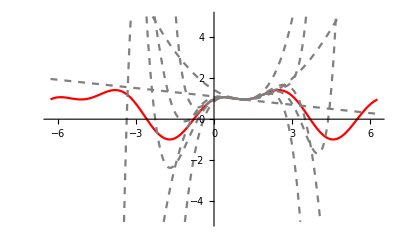

```mathematica
f[x_]:=Sin[x]+Cos[x+0.2]^2;
D[f[x],{x,2}]/.x->5
T[x_,a_,n_]:=Sum[(D[f[t],{t,i}]/.t->a)/(i!)(x-a)^i,{i,0, n}]
Plot[{
f[x],
T[x,1,1],
T[x,1,2],
T[x,1,3],
T[x,1,4],
T[x,1,5],
T[x,1,6],
T[x,1,7],
},
 {x,-2π,2π}, PlotRange->{-5,5}, PlotStyle->{Red, {Gray, Dashed}, {Gray, Dashed},{Gray, Dashed}, {Gray, Dashed}, {Gray, Dashed}, {Gray, Dashed}, {Gray, Dashed}}]
```

Úloha 5:

```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["output.csv", "CSV"]
```

{{-1.,1.},{-0.8,0.64},{-0.6,0.36},{-0.4,0.16},{-0.2,0.04},{0.,0.},{0.2,0.04},{0.4,0.16},{0.6,0.36},{0.8,0.64},{1.,1.}}

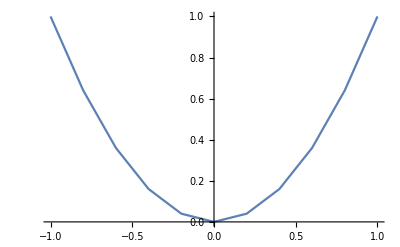

```mathematica
ListLinePlot[data]
```